```mathematica
(*The Syntax of the Mathematica Language*)
(*The operator has higher precedence than,so in both cases Times is the innermost function.*)
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
(*The // operator has rather low precedence.*)
a*b+c//f
```

f[a b+c]

```mathematica
(*The @ operator has high precedence.*)
f@a*b+c
```

c+b f[a]

```mathematica
(*Inserting parentheses makes Plus rather than Times the innermost function.*)
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
(*Operator precedences are such that this requires no parentheses.*)
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m
```

∀_x∃_y x⊗y≻y&&m≠0⇒n⧐̸m

```mathematica
(*FullForm shows the structure of the expression that was constructed.*)
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m;
FullForm[%]
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
(*Note that the first and second forms here are identical;the third requires explicit parentheses.*)
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
(*Plus is a Flat function,so no grouping is necessary here.*)
FullForm[a+b+c+d]
```

Plus[a,b,c,d]

```mathematica
(*Power is not Flat,so the operands have to be grouped in pairs.*)
FullForm[a^b^c^d]
```

Power[a,Power[b,Power[c,d]]]

```mathematica
(*is an infix operator.*)
a⊕b⊕c//FullForm
```

CirclePlus[a,b,c]

```mathematica
(* X (multiplication) is an infix operator which means the same as.&*)
a*a*a*b*b*c
```

a^3 b^2 c

```mathematica
(*The and form parts of a compound operator.*)
∫k[x] ⅆx//FullForm
```

Integrate[k[x],x]

```mathematica
(*No parentheses are needed here:the "inner precedence" of is lower than Times.*)

∫a[x] b[x] ⅆx+c[x]
```

c[x]+∫a[x] b[x]ⅆx

```mathematica
(*Parentheses are needed here,however.*)
∫(a[x]+b[x]) ⅆx+c[x]
```

c[x]+∫(a[x]+b[x])ⅆx

```mathematica
(*This superscript is interpreted as a power.*)
x^(a+b)
```

x^(a+b)

```mathematica
(*dx f ,*is a two-dimensional compound operator.*)
D[x^n, x]
```

n x^(-1+n)

```mathematica
(*sigma is part of a more complicated two-dimensional compound operator.*)
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
(*The sigma  operator has higher precedence than +.*)

∑_(n=1)^∞ 1/n^s + n
```

n+Zeta[s]

```mathematica
(*The Meaning of Expressions*)
(*Expressions in Mathematica are often used to specify operations.So,for example,typing in causes and to be added together,while Factor[x^6-1] performs factorization.Perhaps an even more important use of expressions in Mathematica,however,is to maintain a structure,which can then be acted on by other functions.An expression like does not specify an operation.It merely maintains a list structure,which contains a collection of three elements.Other functions,such as Reverse or Dot,can act on this structure.The full form of the expression is List[a,b,c].The head List performs no operations.Instead,its purpose is to serve as a "tag" to specify the "type" of the structure.You can use expressions in Mathematica to create your own structures.For example,you might want to represent points in three-dimensional space,specified by three coordinates.You could give each point as.The "function" again performs no operation.It serves merely to collect the three coordinates together,and to label the resulting object as a.You can think of expressions like as being "packets of data",tagged with a particular head.Even though all expressions have the same basic structure,you can distinguish different "types" of expressions by giving them different heads.You can then set up transformation rules and programs which treat different types of expressions in different ways.*)
```

```mathematica
(*The Four Kinds of Bracketing in Mathematica*)
```

```mathematica
(*When the expressions you type in are complicated,it is often a good idea to put extra space inside each set of brackets.This makes it somewhat easier for you to see matching pairs of brackets.is,for example,  easier to recognize than.*)
```

```mathematica
(*How to|Use Brackets and Braces Correctly*)

(*You use parentheses in Mathematica for grouping expressions and to determine the precedence of operations:*)
1+2/3
```

5/3

```mathematica
(1+2)/3
```

1

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
(*Anything in Mathematica can be used in lists,including numbers,variables,typeset mathematical expressions,and strings*)
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
```

{1,b,2,3,3 x==12,√(9+y),hello}

```mathematica
(*Lists can contain other lists to create nested lists:*)
```

```mathematica
{1,1,{3,4,5},{3,2}}
```

{1,1,{3,4,5},{3,2}}

```mathematica
(*the functions Range,Sin,and N are used here with square brackets enclosing their arguments:*)
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Sin[2]
```

Sin[2]

```mathematica
N[Sin[2]]
```

0.909297

```mathematica
(*Mathematica uses double square brackets as the short form for the Part function,which is used to get parts of lists*)
v =Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
v[[3]]
```

9

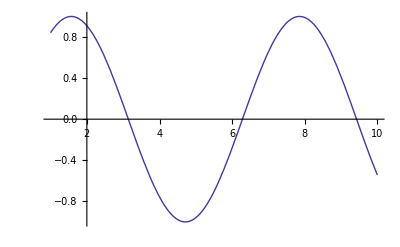

```mathematica
(*plot *)
Plot[Sin[x],{x,1,10}]
```

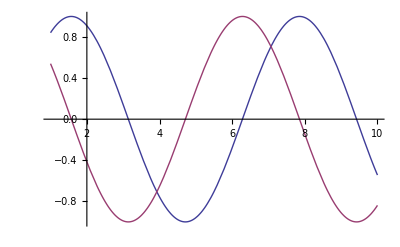

```mathematica
Plot[{Sin[x],Cos[x]},{x,1,10}]
```

```mathematica
(*Symbolic Analysis*)
3 + 62 -1
```

64

```mathematica
3 x-x+2
```

2+2 x

```mathematica
(*You can type any algebraic expression into Mathematica*)
-1+2 x+x^3
```

-1+2 x+x^3

```mathematica
(*Mathematica automatically carries out basic algebraic simplifications.Here it combines and to get.*)
x^2+x-4 x^2
```

x-3 x^2

```mathematica
(*Mathematica rearranges and combines terms using the standard rules of algebra.*)
x y+2 x^2 y+y^2 x^2-2 y x
```

-x y+2 x^2 y+x^2 y^2

```mathematica
(x+2 y+1) (x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
(*The function Expand multiplies out products and powers.*)
(x+2 y+1) (x-2)^2;
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
(*Factor does essentially the inverse of Expand.*)

3+62-1;
Expand[%];
Factor[%]
```

64

```mathematica
(*Here is a more complicated formula,requiring several parentheses.*)
Sqrt[2]/9801 (4 n)! (1103+26390 n)/(n!^4 396^(4 n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
(*Mathematica uses standard rules of algebra to replace by.*)
Sqrt[1+x]^4
```

(1+x)^2

```mathematica
(*Mathematica knows no rules for this expression,so it leaves the expression in the original form you gave.*)
```

```mathematica
Log[1+Cos[x]]
```

Log[1+Cos[x]]

```mathematica
(*Values for Symbols*)
(*This uses the transformation rule in the expression.*)
1+2 x/.x->3
```

7

```mathematica
1+x+x^2/.x->2-y
```

3+(2-y)^2-y

```mathematica
x->3+y
```

x→3+y

```mathematica
x->3+y;
x^2-9/.%
```

-9+(3+y)^2

```mathematica
1+1
```